# -Graphics-

```mathematica
Clear[X,h]
subst={Rc->9.635/2,Rtj->3.25}
eq1=V==Rtj^2 Csc[X/(2 Rtj)]-Rc^2 Csc[X/(2 Rc)]+X/2 (Rc Sqrt[1-X^2/(4 Rc^2)]-Rtj Sqrt[1-X^2/(4 Rtj^2)])
eq2=h== Rtj-Rc+1/2 (Sqrt[4 Rc^2 +X^2]-Sqrt[4 Rtj^2 -X^2])
```

{Rc→4.8175,Rtj→3.25}

V==1/2 X (Rc √(1-X^2/(4 Rc^2))-Rtj √(1-X^2/(4 Rtj^2)))-Rc^2 Csc[X/(2 Rc)]+Rtj^2 Csc[X/(2 Rtj)]

h==-Rc+Rtj+1/2 (-√(4 Rtj^2-X^2)+√(4 Rc^2+X^2))

```mathematica
eq1/.subst
eq2/.subst
```

V==1/2 X (-3.25 √(1-0.0236686 X^2)+4.8175 √(1-0.010772 X^2))-23.2083 Csc[0.103788 X]+10.5625 Csc[0.153846 X]

h==-1.5675+1/2 (-√(42.25-X^2)+√(92.8332+X^2))

```mathematica
Clear[X,h]
subst={Rc->9.635/2,Rtj->3.25}
eq1=V-(Rtj^2 Csc[X/(2 Rtj)]-Rc^2 Csc[X/(2 Rc)]+X/2 (Rc Sqrt[1-X^2/(4 Rc^2)]-Rtj Sqrt[1-X^2/(4 Rtj^2)]))
eq2=h-( Rtj-Rc+1/2 (Sqrt[4 Rc^2 +X^2]-Sqrt[4 Rtj^2 -X^2]))
```

{Rc→4.8175,Rtj→3.25}

V-1/2 X (Rc √(1-X^2/(4 Rc^2))-Rtj √(1-X^2/(4 Rtj^2)))+Rc^2 Csc[X/(2 Rc)]-Rtj^2 Csc[X/(2 Rtj)]

h+Rc-Rtj+1/2 (√(4 Rtj^2-X^2)-√(4 Rc^2+X^2))

```mathematica
eq1/.subst
eq2/.subst
```

V-1/2 X (-3.25 √(1-0.0236686 X^2)+4.8175 √(1-0.010772 X^2))+23.2083 Csc[0.103788 X]-10.5625 Csc[0.153846 X]

1.5675+h+1/2 (√(42.25-X^2)-√(92.8332+X^2))

```mathematica
Cos[1]^-1
```

Sec[1]

```mathematica
0.00023/283
```

8.12721×10^-7

```mathematica
<<Units`
Convert[1 Meter,1.Inch]
```

39.3701 Inch

```mathematica
(6+3/8.)/2
```

3.1875

```mathematica
eq1=H/k μ Fn x
eq2=rtj^2 (θ-Sin[θ]Cos[θ])
subst1={x->t ωtj/p,Fn->Fa/R Ltj, R->100 180/(Pi DLS)}
subst2={θ->Pi - Sec[(a^2 + rtj^2 -r0^2)/(2 a rtj)],a->r0-(rtj-delta)}
numeric={H->312 10^3,k->0.20,DLS->2,Fa->100000,Ltj->40,ωtj->120,t->29.30,p->20,μ->64 10^-6,r0->5,rtj->(6+3/8.)/2}
eq1/.subst1
eq2=eq2//.subst2
eq1=eq1//.subst1/.numeric
eq2=eq2//.subst2/.numeric//N
```

Fn kh x μ

rtj^2 (θ-Cos[θ] Sin[θ])

{x→(t ωtj)/p,Fn→(Fa Ltj)/R,R→18000/(DLS π)}

{θ→π-Sec[(a^2-r0^2+rtj^2)/(2 a rtj)],a→delta+r0-rtj}

{kh→8.1×10^-10,DLS→2,Fa→100000,Ltj→40,ωtj→120,t→2,p→20,μ→1/15625,r0→5,rtj→3.1875}

(Fa kh Ltj t μ ωtj)/(p R)

rtj^2 (π-Sec[(-r0^2+(delta+r0-rtj)^2+rtj^2)/(2 (delta+r0-rtj) rtj)]+Cos[Sec[(-r0^2+(delta+r0-rtj)^2+rtj^2)/(2 (delta+r0-rtj) rtj)]] Sin[Sec[(-r0^2+(delta+r0-rtj)^2+rtj^2)/(2 (delta+r0-rtj) rtj)]])

8.68588×10^-10

10.1602 (3.14159-1. Sec[(0.156863 (-14.8398+(1.8125+delta)^2))/(1.8125+delta)]+Cos[Sec[(0.156863 (-14.8398+(1.8125+delta)^2))/(1.8125+delta)]] Sin[Sec[(0.156863 (-14.8398+(1.8125+delta)^2))/(1.8125+delta)]])

```mathematica
CircJoint=2 Pi (6+3/8.)/2
```

20.0277

```mathematica
Clear[F]
Nrev=211000;
L=CircJoint Nrev
eq1=Ef k/H μ F L
eq2=rtj^2 (θ-Sin[θ]Cos[θ])
subst1={x->t ωtj/p, R->100 180/(Pi DLS)}
subst2={θ->Pi - Sec[(a^2 + rtj^2 -r0^2)/(2 a rtj)],a->r0-(rtj-delta)}
numeric={Ef->2.5 10^-4,H->312 10^3,k->0.20,DLS->2,F->1050,Ltj->40,ωtj->120,t->29.30,p->20,μ->64 10^-6,r0->5,rtj->(6+3/8.)/2}
eq1/.subst1
eq2=eq2//.subst2
eq1=eq1//.subst1/.numeric
eq2=eq2//.subst2/.numeric//N
```

4.22583×10^6

(4.22583×10^6 Ef F k μ)/H

rtj^2 (θ-Cos[θ] Sin[θ])

{x→(t ωtj)/p,R→18000/(DLS π)}

{θ→π-Sec[(a^2-r0^2+rtj^2)/(2 a rtj)],a→delta+r0-rtj}

{Ef→0.00025,H→312000,k→0.2,DLS→2,F→1050,Ltj→40,ωtj→120,t→29.3,p→20,μ→1/15625,r0→5,rtj→3.1875}

(4.22583×10^6 Ef F k μ)/H

rtj^2 (π-Sec[(-r0^2+(delta+r0-rtj)^2+rtj^2)/(2 (delta+r0-rtj) rtj)]+Cos[Sec[(-r0^2+(delta+r0-rtj)^2+rtj^2)/(2 (delta+r0-rtj) rtj)]] Sin[Sec[(-r0^2+(delta+r0-rtj)^2+rtj^2)/(2 (delta+r0-rtj) rtj)]])

0.000045509

10.1602 (3.14159-1. Sec[(0.156863 (-14.8398+(1.8125+delta)^2))/(1.8125+delta)]+Cos[Sec[(0.156863 (-14.8398+(1.8125+delta)^2))/(1.8125+delta)]] Sin[Sec[(0.156863 (-14.8398+(1.8125+delta)^2))/(1.8125+delta)]])

```mathematica
NSolve[eq2==eq1,delta]
```

$Aborted

```mathematica
Table[(eq2-eq1)/.delta->i,{i,3,8,0.1}]
```

{22.7527,22.6272,22.4895,22.3389,22.1751,21.9972,21.8047,21.5967,21.3723,21.1304,20.8701,20.59,20.2889,19.9652,19.6176,19.2442,18.8433,18.413,17.9513,17.456,16.9249,16.3558,15.7464,15.0945,14.3982,13.6554,12.865,12.026,11.1387,10.2045,9.22651,8.21005,7.16356,6.09917,5.03374,3.98968,2.99561,2.08644,1.30196,0.682948,0.262458,0.0493948,0.000181145,-0.0253303,-0.323003,-1.40146,-3.97728,-8.76515,-15.8305,-23.4609,-27.9033}

```mathematica
driv=D[eq2-eq1,delta];
```

```mathematica
FindRoot[(eq2-eq1),{delta,3.}]
```

{delta→7.21373}

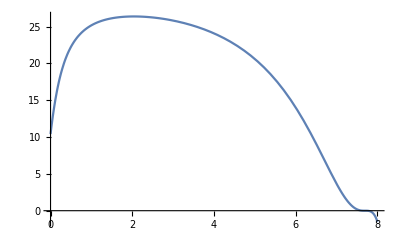

```mathematica
Plot[(eq2-eq1),{delta,0,8}]
```

# -Graphics-

```mathematica
Clear[F,L,Nrev]
L=PerimTJ Nrev
Eff==V H/(K F L)
V==Eff Ff L/H
```

Nrev PerimTJ

Eff==(H V)/(F K Nrev PerimTJ)

V==(Eff Ff Nrev PerimTJ)/H

```mathematica
200 10^9 0.81 10^-9
```

162.

```mathematica
(6+3/8.)/2
```

3.1875

```mathematica
Nrev=214000.;
rtj=(6+3/8.)/2;
t=29.7 60;
Nrev/t
PerimTj=2 Pi rtj
L=Nrev PerimTj
Fa=1960.
Fn=0.2 Fa
Energy=Fn L
EH=0.81 10^-9
Energy EH
```

120.09

20.0277

4.28592×10^6

1960.

392.

1.68008×10^9

8.1×10^-10

1.36086

```mathematica
2 Pi rtj
```

20.0277

```mathematica
Nrev=10000000;
rtj=(6+3/8.)/2;
t=29.7 60;
Nrev/t
PerimTj=2 Pi rtj
L=Nrev PerimTj
Fa=4000.
Fn=0.25 Fa
Energy=Fn L
EH=0.81 10^-9
Energy EH
```

5611.67

20.0277

2.00277×10^8

4000.

1000.

2.00277×10^11

8.1×10^-10

162.224

# -Graphics-

0.00866059

10.1602 (π-Sec[(0.156863 (-82.4805+(6.4375+delta)^2))/(6.4375+delta)]+Cos[Sec[(0.156863 (-82.4805+(6.4375+delta)^2))/(6.4375+delta)]] Sin[Sec[(0.156863 (-82.4805+(6.4375+delta)^2))/(6.4375+delta)]])

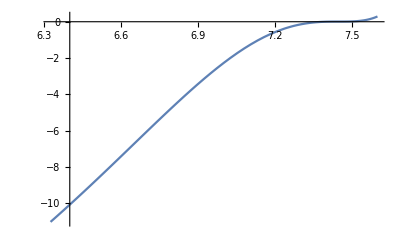

{delta→7.3965}

```mathematica
eq1= (k Fn x)/H;
subst1={x->L w rtj/(v p),Fn->Fa/R Ltj};
subst2={R->100 180/(Pi DLS)};
eq2=rtj^2 (θ-Sin[θ]Cos[θ]);
subst3={θ->Pi - Sec[((r0-(rtj-delta))^2 + rtj^2 -r0^2)/(2 (r0-(rtj-delta)) rtj)]};
numeric={rtj->(6+3/8.)/2,r0->9.625,DLS->2,Fa->4000,Ltj->20.02,w->120,L->1,p->1,v->1,H->283.951,k->0.00023};
eq1=eq1/.subst1/.subst2/.numeric
eq2=eq2/.subst3/.numeric
Plot[eq1-eq2,{delta,6.325,7.6}]
FindRoot[eq1-eq2,{delta,6}]
```

```mathematica
eq1
```

0.00866059

```mathematica
eq2/.delta->0.01
```

10.6681

```mathematica
eq1-eq2
```

(Fn k x)/H-rtj^2 (θ-Cos[θ] Sin[θ])

# -Graphics-

# -Graphics-

```mathematica
(*Nrev=10000000;
rtj=(6+3/8.)/2;
t=29.7 60;*)
(*Fa=4000.
Fn=0.25 Fa*)


s1={Energy->Fn L}
s2={L->Nrev PerimTj}
s3={PerimTj->2 Pi rtj}
s4={Fn->μ Fa}
(*EH=0.81 10^-9*)
numeric={Fa->4000,μ->0.25,rtj->(6+3/8.)/2,EH->0.81 10^-9,Nrev->10000000,r0->9.625/2}
eq1=0.01Energy EH/.s1/.s2/.s3/.s4
eq1=eq1/.numeric
```

{Energy→Fn L}

{L→Nrev PerimTj}

{PerimTj→2 π rtj}

{Fn→Fa μ}

{Fa→4000,μ→0.25,rtj→3.1875,EH→8.1×10^-10,Nrev→10000000,r0→4.8125}

0.0628319 EH Fa Nrev rtj μ

1.62224

```mathematica
eq2=rtj^2 (θ-Sin[θ]Cos[θ]);
subst3={θ->Pi - Sec[((r0-(rtj-delta))^2 + rtj^2 -r0^2)/(2 (r0-(rtj-delta)) rtj)]};
eq2=eq2/.subst3/.numeric
```

10.1602 (π-Sec[(0.156863 (-13.+(1.625+delta)^2))/(1.625+delta)]+Cos[Sec[(0.156863 (-13.+(1.625+delta)^2))/(1.625+delta)]] Sin[Sec[(0.156863 (-13.+(1.625+delta)^2))/(1.625+delta)]])

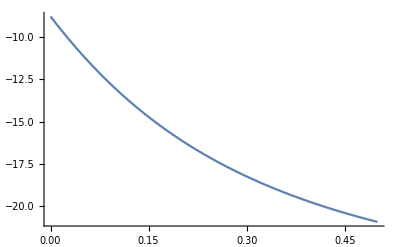

{delta→-0.157947}

{-24.756,{delta→1.98055}}

```mathematica
Plot[eq1-eq2,{delta,0,0.5}]
FindRoot[eq1-eq2,{delta,0}]
FindMinimum[eq1-eq2,{delta,0}]
```

```mathematica
0.5/60
```

0.00833333

```mathematica
1/0.00833
```

120.048

```mathematica
2.0027653166634932*^8/(120 6.325)
```

263869.

```mathematica
263869./(60 60)
```

73.2969

```mathematica
<<Units`
Convert[1Feet/Second,1Feet]
```

(Fa k rtj t w μ)/(H p)

22.7092

10.1602 (π-Sec[(0.156863 (-13.+(1.625+delta)^2))/(1.625+delta)]+Cos[Sec[(0.156863 (-13.+(1.625+delta)^2))/(1.625+delta)]] Sin[Sec[(0.156863 (-13.+(1.625+delta)^2))/(1.625+delta)]])

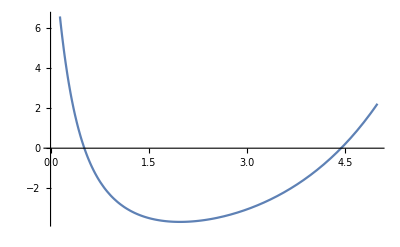

{delta→4.44404}

```mathematica
eq1= k Fn x/H;
(*subst1={x-> t w rtj/( p),Fn->Fa/R Ltj};*)
subst1={x-> t w rtj/( p),Fn->Fa μ};
subst2={R->100 180/(Pi DLS)};
eq2=rtj^2 (θ-Sin[θ]Cos[θ]);
subst3={θ->Pi - Sec[((r0-(rtj-delta))^2 + rtj^2 -r0^2)/(2 (r0-(rtj-delta)) rtj)]};
numeric={μ->0.25,rtj->(6+3/8.)/2,r0->9.625/2,DLS->2,Fa->4000.,Ltj->20.02,w->120,p->1,H->283.951,k->0.00023,t->263869/(60 60)};
eq1=eq1/.subst1
eq1=eq1/.numeric
eq2=eq2/.subst3/.numeric
Plot[eq1-eq2,{delta,0,5}]
FindRoot[eq1-eq2,{delta,6}]
```

```mathematica
1/R t w rtj/.subst2/.subst3/.numeric
```

9.78644

```mathematica
60t w rtj/.numeric
```

1.68216×10^6

```mathematica
(120 (6+3/8.)/2)/200 10^6
```

1.9125×10^6

```mathematica
1/3000. 30000
```

10.

```mathematica
100 180/(Pi 2.)
```

2864.79

```mathematica
(6+3/8.)
```

6.375

```mathematica
V=EH  Fn L
subst1={L-> 2 Pi rtj Nrev,Fn->Fa μ};
numeric={μ->0.25,rtj->6.375/2,Fa->4000.,Nrev->10000000,EH->0.81 10^-9};
```

EH Fn L

```mathematica
V/.subst1/.numeric
L/.subst1/.numeric
V/.subst1
```

162.224

2.00277×10^8

2 EH Fa Nrev π rtj μ

```mathematica
2 EH Fa Nrev π rtj μ
```

```mathematica
eq1= k Fn x/H;
(*subst1={x-> t w rtj/( p),Fn->Fa/R Ltj};*)
subst1={x-> t w rtj/( p),Fn->Fa μ};
subst2={R->100 180/(Pi DLS)};
eq2=rtj^2 (θ-Sin[θ]Cos[θ]);
subst3={θ->Pi - Sec[((r0-(rtj-delta))^2 + rtj^2 -r0^2)/(2 (r0-(rtj-delta)) rtj)]};
numeric={μ->0.25,rtj->(6+3/8.)/2,r0->9.625/2,DLS->2,Fa->4000.,Ltj->20.02,w->120,p->1,H->283.951,k->0.00023,t->556955};
```

```mathematica
x/.subst1/.numeric
```

2.13035×10^8

```mathematica
tt=200227 10^3/120 2 Pi 6.375/2
```

3.34173×10^7

```mathematica
tt/60
```

556955.

```mathematica
10000000 2 Pi 6.375/2
```

2.00277×10^8

```mathematica
Integrate[(a+Sqrt[rtj^2-x^2]-Sqrt[rc^2-x^2]),{x,0,1}]
```

$Aborted

a-rc+rtj

√(rc^2-((a^2+rc^2-rtj^2)^2)/(4 a^2))

a d-rc^2 ArcSin[d/rc]+rtj^2 ArcSin[d/rtj]

a √(rc^2-((a^2+rc^2-rtj^2)^2)/(4 a^2))-rc^2 ArcSin[(√(rc^2-((a^2+rc^2-rtj^2)^2)/(4 a^2)))/rc]+rtj^2 ArcSin[(√(rc^2-((a^2+rc^2-rtj^2)^2)/(4 a^2)))/rtj]

{Fa→4000,μ→0.25,rtj→3.1875,EH→8.1×10^-10,Nrev→10000000,rc→4.8125}

1/500 EH Fa Nrev π rtj μ

0.162224

a √(23.1602-((13.+a^2)^2)/(4 a^2))-23.1602 ArcSin[0.207792 √(23.1602-((13.+a^2)^2)/(4 a^2))]+10.1602 ArcSin[0.313725 √(23.1602-((13.+a^2)^2)/(4 a^2))]

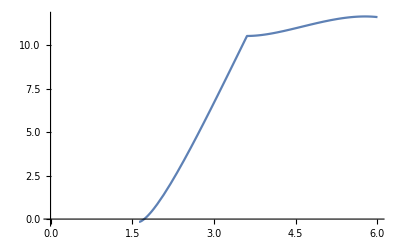

{a→1.71888}

```mathematica
eqDW=a-rc+rtj
eqd=Sqrt[rc^2 -((rc^2 + a^2 - rtj^2)^2) /(4 a^2)]
eqS1=(rtj^2 ArcSin[d/rtj]-rc^2 ArcSin[d/rc]+d a)
eqS1=eqS1/.d->eqd
numeric={Fa->4000,μ->0.25,rtj->(6+3/8.)/2,EH->0.81 10^-9,Nrev->10000000,rc->9.625/2}
eqS=EH μ Fa Nrev Pi 2rtj/1000
eqS=eqS/.numeric
eqS1=eqS1/.numeric
Plot[eqS1-eqS,{a,0,6}]
FindRoot[eqS1-eqS,{a,2}]
```

2 EH Fa Nrev π rtj μ

12 (2 √(P (P-R) (P-rtj) (P-S))-R^2 α+rtj^2 β)

ArcCos[(R^2-rtj^2+S^2)/(2 R S)]

ArcTan[(R √(1-((R^2-rtj^2+S^2)^2)/(4 R^2 S^2)))/(-S+(R^2-rtj^2+S^2)/(2 S))]

1/2 (R+rtj+S)

h+R-rtj

{rtj→3.1875,Nrev→10000000,μ→0.25,Fa→4000,EH→8.1×10^-10,R→3.7}

1.62224

12 (2 √(P (P-R) (P-rtj) (P-S))-R^2 ArcCos[(R^2-rtj^2+S^2)/(2 R S)]+rtj^2 ArcTan[(R √(1-((R^2-rtj^2+S^2)^2)/(4 R^2 S^2)))/(-S+(R^2-rtj^2+S^2)/(2 S))])

12 (√2 √((7.4+h) (-3.7+1/2 (7.4+h)) (-3.1875+1/2 (7.4+h)) (-0.5125-h+1/2 (7.4+h)))-13.69 ArcCos[(0.135135 (3.52984+(0.5125+h)^2))/(0.5125+h)]+10.1602 ArcTan[(3.7 √(1-(0.0182615 (3.52984+(0.5125+h)^2)^2)/(0.5125+h)^2))/(-0.5125-h+(3.52984+(0.5125+h)^2)/(2 (0.5125+h)))])

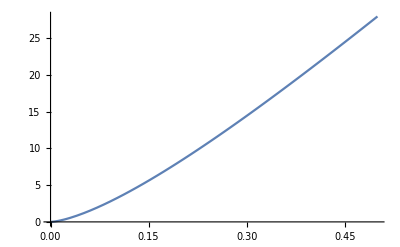

```mathematica
eqWV1=EH Fa μ Pi 2 rtj Nrev
eqWV=12(β rtj^2 + 2 Sqrt[P(P-R)(P-rtj)(P-S)]-α R^2)
alfaeq=ArcCos[(R^2 + S^2 - rtj^2)/(2 R S)]
betaeq=ArcTan[R Sin[α]/(R Cos[α]-S)]/.α->alfaeq
Peq=(R+rtj+S)/2
Seq=R-(rtj-h)
numeric={rtj->(6+3/8.)/2,Nrev->10000000,μ->0.25,Fa->4000,EH->0.81 10^-9,R->3.7}
eqWV1=0.01eqWV1/.numeric
eqWV=eqWV/.{β->betaeq,α->alfaeq}
eqWV=eqWV/.P->Peq/.S->Seq/.numeric
Plot[eqWV,{h,0,0.5}]
```

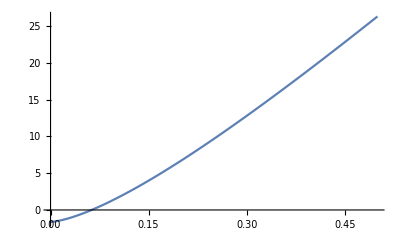

{h→0.0628438}

```mathematica
Plot[eqWV-eqWV1,{h,0,0.5}]
FindRoot[eqWV-eqWV1,{h,0.5}]
```